```mathematica
(* Import data from Johns Hopkins *)
HopkinsConfirmed = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_confirmed_global.csv",CharacterEncoding->"UTF8"],1];
HopkinsRecovered = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_recovered_global.csv",CharacterEncoding->"UTF8"],1];
HopkinsDeaths = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_deaths_global.csv",CharacterEncoding->"UTF8"],1];
CountryList=AlphabeticSort[DeleteDuplicates[Transpose[HopkinsConfirmed][[2]]]];
Export[NotebookDirectory[]<>"/countries.xls",TableForm[Table[{i,CountryList[[i]]},{i,1,Length[CountryList]}]],"XLS"];
```

```mathematica
(* Data for countries can be split over multiple rows in the data from Hopkins *)
DataByCountry = Table[{},{i,1,Length[CountryList]}];
NumberOfDays = Length[Transpose[HopkinsConfirmed]]-4;

For[country = 1, country ≤ Length[CountryList],country++,
TempConfirmed=Table[0,{i,1,NumberOfDays}];
TempRecovered = Table[0,{i,1,NumberOfDays}];
TempDeaths = Table[0,{i,1,NumberOfDays}];
For[row=1,row≤ Length[HopkinsConfirmed],row++,
If[StringMatchQ[CountryList[[country]], HopkinsConfirmed[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempConfirmed = TempConfirmed + Drop[HopkinsConfirmed[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsRecovered],row++,
If[StringMatchQ[CountryList[[country]], HopkinsRecovered[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempRecovered= TempRecovered + Drop[HopkinsRecovered[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsDeaths],row++,
If[StringMatchQ[CountryList[[country]], HopkinsDeaths[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempDeaths = TempDeaths + Drop[HopkinsDeaths[[row]],4];
]
];
TempConfirmedDiff=TempConfirmed-Drop[Join[{0},TempConfirmed],-1];
TempRecoveredDiff=TempRecovered-Drop[Join[{0},TempRecovered],-1];
TempDeathsDiff=TempDeaths-Drop[Join[{0},TempDeaths],-1];
DataByCountry[[country]]= {ToString[CountryList[[country]]],TempConfirmed,TempRecovered,TempDeaths,TempConfirmedDiff,TempRecoveredDiff,TempDeathsDiff};
]
```

```mathematica
(* Model *)
SIR[country_,dday_] := (
n=n0;
i=i0;
r=0;
m=0;
c=r+r+m;
s = n-i-r-m;
cost = 0;
For[sirday=1,sirday≤ dday, sirday++,
lambda = gamma * listr0[[sirday]][[2]];
ds = -lambda i *(s/n);
di = lambda i * (s/n) -gamma i - delta i;
dr = gamma i;
dm = delta i;
dc=di +dr+dm;
s+=ds;
i+=di;
r+=dr;
m+=dm;
c+=dc;
n=s+i+r;
If[sirday≤ Length[DataByCountry[[country]][[2]]],
cost = cost + (c-DataByCountry[[country]][[2]][[sirday]])^2;];
];
Return[{s,i,r,m,c,cost,di,dm}];
);
```

```mathematica
(* Initial values for this country *)
Window =3;(* Number of days over which to fit the model *)
future=30; (* Number of days to project ahead *)
```

```mathematica
CountrySIR[country_] := (
CurrentCountry =country;
today = Length[DataByCountry[[CurrentCountry]][[2]]];
CFR=DataByCountry[[CurrentCountry]][[4]][[-1]]/DataByCountry[[CurrentCountry]][[2]][[-1]];

n0 = 11400000;
i0=100;
gamma=(1-CFR)/12.4;
delta = CFR/10.4;
listr0 = {};
For[day = 1, day <= Length[DataByCountry[[CurrentCountry]][[2]]] + 60, day++,
  listr0 = Join[listr0, {{day, 4.3}}];
  ];

(* Fit model to the data *)
For[day=1,day≤Length[DataByCountry[[CurrentCountry]][[2]]]-Window,day++,
bestr0=listr0[[day]][[2]];
bestcost=SIR[CurrentCountry,day+Window][[6]];
For[kr0 = 0.05,kr0≤7,kr0=kr0+0.05,
(* set this possible r0 for all following days and see what the cost is *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] = kr0;];
temp=SIR[CurrentCountry,day + Window];
If[temp[[6]]<bestcost,bestcost=temp[[6]];bestr0=kr0;];
];

(* We found a good r0 for this day, set it for all the following days *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] =bestr0;];
];

(* Generate the lists of data for the plots *)
lists={};
listi={};
listr={};
listm={};
listc={};
listdi={};
listdm={};
For[day=1,day≤Length[DataByCountry[[CurrentCountry]][[2]]]+60,day++,
temp=SIR[CurrentCountry,day];
lists=Append[lists,{day,temp[[1]]}];
listi=Append[listi,{day,temp[[2]]}];
listr=Append[listr,{day,temp[[3]]}];
listm=Append[listm,{day,temp[[4]]}];
listc=Append[listc,{day,temp[[5]]}];
listdi=Append[listdi,{day,temp[[7]]}];
listdm=Append[listdm,{day,temp[[8]]}];
];
Return[{CurrentCountry,DataByCountry[[CurrentCountry]][[1]],listr0}];
);
```

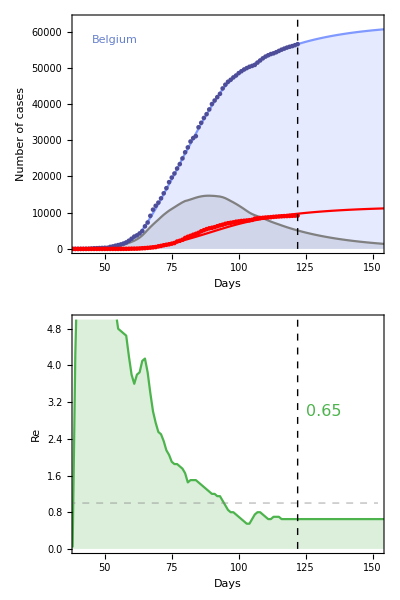

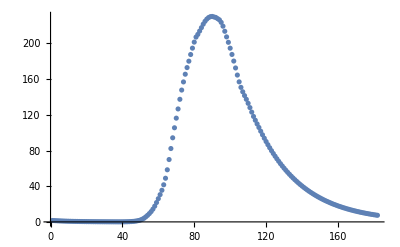

```mathematica
CountrySIR[17];

(* Generate plots *)
height=Max[ {Max[Drop[listc,-55]],Max[DataByCountry[[CurrentCountry]][[2]]]}];

If[listr0[[-1]][[2]]<0.8,R0Color=RGBColor[0.3,0.7,0.3],If[listr0[[-1]][[2]]>1.2,R0Color=RGBColor[0.7,0.3,0.3],R0Color=RGBColor[0.9,0.7,0.3]]];

plotFinalR0 = Graphics[{Text[Style[listr0[[-1]][[2]], FontSize->16,R0Color],{today+3,3},{Left,Center}]}];

plotLine = Graphics[Style[Line[{{0, 1}, {today+future, 1}}],Dashed,RGBColor [0.5,0.5,0.5,0.5]]];

plotCountryname = Graphics[{Text[Style[DataByCountry[[CurrentCountry]][[1]], Large,RGBColor[0.4,0.5,0.8]],{45,1.00height},{Left,Center}]}];

plotModel=Show[{ListPlot[{listi,listc,DataByCountry[[CurrentCountry]][[2]],DataByCountry[[CurrentCountry]][[4]],listm},PlotRange->{{40,today+future},{0,1.10height}},Joined->{True,True,False,False,True},Filling->{1-> Bottom,2->Bottom},PlotStyle->{Gray,RGBColor[0.5,0.6,1],RGBColor[0.3,0.3,0.6],Red,Red},FrameLabel->{"Days","Number of cases"},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thickness[0.002],13],AspectRatio->1/1,ImageSize->600],plotCountryname}];

plotR0=ListPlot[listr0,Joined->True,Filling->{1->Bottom},PlotStyle->R0Color,FrameLabel->{"Days","Re"},FrameStyle->Directive[Thickness[0.002],13],Frame->True,FrameTicks->Automatic,AspectRatio->1/8,PlotRange->{{40,today+future},{0,5}},ImageSize->600];

ThePlotThickens=Multicolumn[{Show[{plotModel,Graphics[{Dashed, Line[{{today, 0}, {today, 1.2 height}}]}]},ImagePadding->{{70,10},{20,10}}],Show[{plotR0,plotFinalR0,plotLine,Graphics[{Dashed, Line[{{today, 0}, {today, 7}}]}]},ImagePadding->{{70,10},{40,5}}]},1]
CountryFilename=NotebookDirectory[]<>"/results/SIR-" <> ToString[DataByCountry[[CurrentCountry]][[1]]] <> "-" <> DateString[{"ISODate"}] <> ".png";
Export[CountryFilename, ThePlotThickens, ImageResolution -> 600];
ListPlot[listdm]
```

```mathematica
R0PerCountry={};
For[country=1,country≤Length[CountryList],country++,
R0PerCountry = Append[R0PerCountry,CountrySIR[country]];
Print["Country: "<>R0PerCountry[[-1]][[2]]<>" -> "<>ToString[R0PerCountry[[-1]][[3]][[-1]][[2]]]];
]
```

Country: Afghanistan -> 1.8

Country: Albania -> 0.8

Country: Algeria -> 1.2

Country: Andorra -> 0.1

Country: Angola -> 2.

Country: Antigua and Barbuda -> 0.05

Country: Argentina -> 2.1

Country: Armenia -> 1.85

Country: Australia -> 0.45

Country: Austria -> 0.65

Country: Azerbaijan -> 1.45

Country: Bahamas -> 0.3

Country: Bahrain -> 1.35

Country: Bangladesh -> 1.75

Country: Barbados -> 1.05

Country: Belarus -> 1.1

Country: Belgium -> 0.65

Country: Belize -> 0.05

Country: Benin -> 0.05

Country: Bhutan -> 0.75

Country: Bolivia -> 1.9

Country: Bosnia and Herzegovina -> 0.65

Country: Botswana -> 3.5

Country: Brazil -> 1.95

Country: Brunei -> 0.05

Country: Bulgaria -> 0.9

Country: Burkina Faso -> 0.7

Country: Burma -> 1.

Country: Burundi -> 2.9

Country: Cabo Verde -> 0.8

Country: Cambodia -> 0.05

Country: Cameroon -> 2.3

Country: Canada -> 0.95

Country: Central African Republic -> 2.05

Country: Chad -> 1.3

Country: Chile -> 2.05

Country: China -> 0.35

Country: Colombia -> 1.45

Country: Comoros -> 7.

Country: Congo (Brazzaville) -> 1.4

Country: Congo (Kinshasa) -> 1.8

Country: Costa Rica -> 1.15

Country: Cote d'Ivoire -> 1.1

Country: Croatia -> 0.3

Country: Cuba -> 0.5

Country: Cyprus -> 0.45

Country: Czechia -> 0.95

Country: Denmark -> 0.65

Country: Diamond Princess -> 0.05

Country: Djibouti -> 3.6

Country: Dominica -> 0.05

Country: Dominican Republic -> 1.1

Country: Ecuador -> 1.15

Country: Egypt -> 1.8

Country: El Salvador -> 1.5

Country: Equatorial Guinea -> 2.15

Country: Eritrea -> 0.05

Country: Estonia -> 0.65

Country: Eswatini -> 0.85

Country: Ethiopia -> 1.75

Country: Fiji -> 0.05

Country: Finland -> 0.6

Country: France -> 0.5

Country: Gabon -> 1.35

Country: Gambia -> 0.6

Country: Georgia -> 0.7

Country: Germany -> 0.7

Country: Ghana -> 0.8

Country: Greece -> 0.6

Country: Grenada -> 0.2

Country: Guatemala -> 2.2

Country: Guinea -> 1.1

Country: Guinea-Bissau -> 0.75

Country: Guyana -> 0.8

Country: Haiti -> 2.95

Country: Holy See -> 0.05

Country: Honduras -> 1.65

Country: Hungary -> 0.9

Country: Iceland -> 0.05

Country: India -> 1.7

Country: Indonesia -> 1.6

Country: Iran -> 1.45

Country: Iraq -> 1.5

Country: Ireland -> 0.4

Country: Israel -> 0.15

Country: Italy -> 0.6

Country: Jamaica -> 0.7

Country: Japan -> 0.35

Country: Jordan -> 1.6

Country: Kazakhstan -> 1.7

Country: Kenya -> 2.05

Country: Korea, South -> 0.95

Country: Kosovo -> 0.85

Country: Kuwait -> 1.6

Country: Kyrgyzstan -> 1.4

Country: Laos -> 0.05

Country: Latvia -> 0.7

Country: Lebanon -> 2.4

Country: Lesotho -> 0.05

Country: Liberia -> 1.05

Country: Libya -> 2.15

Country: Liechtenstein -> 0.05

Country: Lithuania -> 1.15

Country: Luxembourg -> 0.55

Country: Madagascar -> 2.65

Country: Malawi -> 1.4

Country: Malaysia -> 0.8

Country: Maldives -> 1.

Country: Mali -> 1.2

Country: Malta -> 1.6

Country: Mauritania -> 7.

Country: Mauritius -> 0.05

Country: Mexico -> 1.7

Country: Moldova -> 1.25

Country: Monaco -> 0.45

Country: Mongolia -> 1.45

Country: Montenegro -> 0.05

Country: Morocco -> 0.75

Country: Mozambique -> 1.5

Country: MS Zaandam -> 0.05

Country: Namibia -> 7.

Country: Nepal -> 2.15

Country: Netherlands -> 0.65

Country: New Zealand -> 0.25

Country: Nicaragua -> 7.

Country: Niger -> 0.75

Country: Nigeria -> 1.3

Country: North Macedonia -> 1.2

Country: Norway -> 0.45

Country: Oman -> 1.8

Country: Pakistan -> 1.5

Country: Panama -> 0.85

Country: Papua New Guinea -> 0.05

Country: Paraguay -> 0.55

Country: Peru -> 1.4

Country: Philippines -> 1.05

Country: Poland -> 1.2

Country: Portugal -> 0.85

Country: Qatar -> 1.4

Country: Romania -> 0.75

Country: Russia -> 1.05

Country: Rwanda -> 1.2

Country: Saint Kitts and Nevis -> 0.05

Country: Saint Lucia -> 0.05

Country: Saint Vincent and the Grenadines -> 1.5

Country: San Marino -> 0.3

Country: Sao Tome and Principe -> 1.05

Country: Saudi Arabia -> 1.45

Country: Senegal -> 1.15

Country: Serbia -> 0.7

Country: Seychelles -> 0.05

Country: Sierra Leone -> 1.35

Country: Singapore -> 0.8

Country: Slovakia -> 0.3

Country: Slovenia -> 0.15

Country: Somalia -> 0.95

Country: South Africa -> 1.7

Country: South Sudan -> 3.2

Country: Spain -> 0.65

Country: Sri Lanka -> 0.9

Country: Sudan -> 1.85

Country: Suriname -> 3.8

Country: Sweden -> 1.2

Country: Switzerland -> 0.3

Country: Syria -> 1.15

Country: Taiwan* -> 0.05

Country: Tajikistan -> 7.

Country: Tanzania -> 0.05

Country: Thailand -> 0.2

Country: Timor-Leste -> 0.05

Country: Togo -> 1.3

Country: Trinidad and Tobago -> 0.05

Country: Tunisia -> 0.35

Country: Turkey -> 0.6

Country: Uganda -> 0.05

Country: Ukraine -> 0.95

Country: United Arab Emirates -> 1.4

Country: United Kingdom -> 0.7

Country: Uruguay -> 0.65

Country: US -> 1.15

Country: Uzbekistan -> 1.1

Country: Venezuela -> 3.3

Country: Vietnam -> 0.6

Country: West Bank and Gaza -> 2.45

Country: Western Sahara -> 0.05

Country: Yemen -> 7.

Country: Zambia -> 1.35

Country: Zimbabwe -> 2.

```mathematica
countryPlotted = {};
For[country=1,country≤Length[CountryList],country++,
countryPlotted=Append[countryPlotted,Entity["Country",StringReplace[ToString[CountryList[[country]]]," " -> ""]]->R0PerCountry[[country]][[3]][[-1]][[2]]];
];
```

```mathematica
WorldMap = GeoRegionValuePlot[countryPlotted,ImageSize->Large,ColorFunction->Function[{z},ColorData["TemperatureMap"][z/2]],ColorFunctionScaling->False,ImageSize->Full]
```

-Graphics-

```mathematica
WorldMapFilename=NotebookDirectory[]<>"/results/SIR-World-map-" <> DateString[{"ISODate"}] <> ".png";
Export[WorldMapFilename, WorldMap, ImageResolution -> 600];
```